```mathematica
(* calculating the complex reflectivity of a chirped FBG with parameters
based on SMART photonics PDK.
Done by Spencer Jolly, B-PHOT Vrije Universiteit Brussel *)
```

```mathematica
ClearAll[c,k,n,lambda,L,F,d,x,y,solution]
```

```mathematica
c=2.9979*10^(8); (*speed of light in vacuum*)
```

```mathematica
k=50*10^(2); (*50 1/cm in SMART PDK*)
```

```mathematica
n=3.266; (*effective refractive index on InP*)
```

```mathematica
lambda=1550*10^(-9); (*telecom wavelength*)
```

```mathematica
L=200*10^(-6); (*chosen length*)
```

```mathematica
BW=3*10^(-9); (*desired bandwidth*)
```

```mathematica
F=(BW*4*3.1415926*n*L)/(lambda^2)
```

10.2498

```mathematica
solution=ParametricNDSolve[{y''[x]-I(2*d-F*x)*y'[x]-((k*L)^2)*y[x]==0,y'[-0.5]==(k*L)*Exp[I*(-d-F/8)],y[0.5]==0},y,{x,-0.5,0.5},{d}]
```

{y→ParametricFunction[<>]}

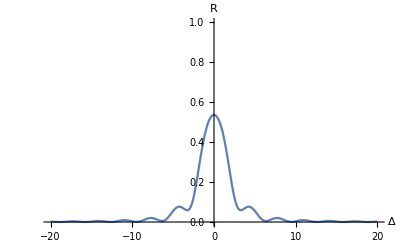

```mathematica
Plot[Evaluate[Abs[(y[d][-0.5]/.solution)]^2],{d,-20,20},PlotRange->{0,1},AxesLabel-> {Δ,R}]
```

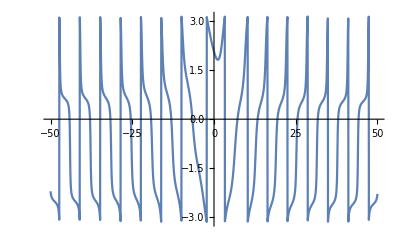

```mathematica
Plot[Evaluate[Arg[(y[d][-0.5]/.solution)]],{d,-50,50},PlotRange->{-3.1415926,+3.1415926}]
```